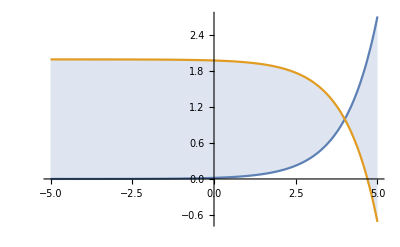

```mathematica
Plot[{Exp[x-4],-Exp[x-4]+2},{x,-5,5},Filling->{1->{2}}]
```

```mathematica
?ShadedRegion
```

Information::notfound: Symbol ShadedRegion not found.

```mathematica
shadeBoundedArea[plot_,region_]:=Module[{rangex,rangey},{rangex,rangey}=PlotRange/.AbsoluteOptions[plot];
Show[plot,RegionPlot[region,Evaluate@{x,Sequence@@rangex},Evaluate@{y,Sequence@@rangey},PerformanceGoal->"Quality",PlotStyle->Directive[Opacity[1],LightYellow]],plot]]

Clear[x,y];
```

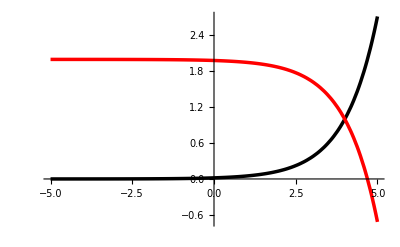

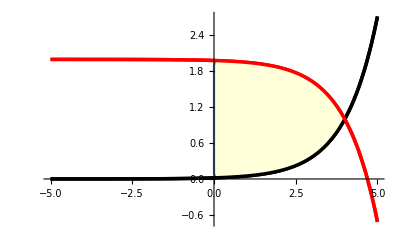

```mathematica
f1[x_]:=Exp[x-4];
f2[x_]:=2-Exp[x-4];
p=Plot[{f1[x],f2[x]},{x,-5,5},PlotStyle->{{Black,Thickness[0.00625]},{Red,Thickness[0.00625]}}]

shadeBoundedArea[p,f1[x]<y<f2[x]&&x>0]
```

```mathematica
Integrate[Integrate[1-x y^2,{y,f2[x],f1[x]}],{x,0,4}]
```

325/54-2/(27 ⅇ^12)+1/(2 ⅇ^8)-6/ⅇ^4